This notebook provides a small, reproducible demonstration of the competing-information diffusion model. 
It generates a communication network, initializes misinformation sources, runs one stochastic simulation, computes selected outcome measures, visualizes the misinformation and official-information trajectories, and exports the resulting demonstration data. 
The configuration is intentionally small and is not intended to reproduce the full production experiments reported in the associated article.

```mathematica
(* ::Section::*)
(*Project setup and module loading*)

ClearAll[$ProjectRoot,$SrcDir,$DemoOutDir,requiredModules,missingModules];

$ProjectRoot=DirectoryName[NotebookDirectory[]];
$SrcDir=FileNameJoin[{$ProjectRoot,"src"}];
$DemoOutDir=FileNameJoin[{$ProjectRoot,"demo_output"}];

requiredModules={"01_TypesAndValidation.wl","02_Networks.wl","03_Initialization.wl","04_Signals.wl","05_UpdateRules.wl","06_SimulationCore.wl","07_Metrics.wl","09_Export.wl"};
missingModules=Select[requiredModules,!FileExistsQ[FileNameJoin[{$SrcDir,#}]]&];
If[missingModules=!={},Print["Missing source modules: ",missingModules];
Abort[];];
Quiet@Check[Scan[Get[FileNameJoin[{$SrcDir,#}]]&,requiredModules],Print["Unable to load the simulation modules."];
Abort[];];

If[!DirectoryQ[$DemoOutDir],CreateDirectory[$DemoOutDir,CreateIntermediateDirectories->True]];
Print["Simulation modules loaded successfully."];
```

Simulation modules loaded successfully.

```mathematica
(* ::Section::*)
(*Demo configuration*)
ClearAll[demoNetSpec,demoParams,parameterValidation,networkValidation];

demoNetSpec=<|"NetworkType"->"SmallWorld","n"->30,"nMedia"->3,"k"->4,"rewiringProbability"->0.1,"MediaAssignmentMethod"->"TopDegree","BoostMediaConnectivity"->True,"MediaDegreeMultiplier"->3,"Seed"->123456,"MediaBoostSeed"->1123456|>;
demoParams=<|"c"->0.45,"d"->0.35,"tau"->5,"Tmax"->40,"R"->1,"Seed"->123456,"SimulationSeed"->555,"muClearance"->0.05,"StoreSignals"->False,"StoreUpdates"->False,"ResampleSourcesPerRun"->False|>;

parameterValidation=ValidateParameters[demoParams];
networkValidation=ValidateNetworkSpec[demoNetSpec];

If[!ValidationSucceededQ[parameterValidation],Print[parameterValidation];
Abort[];];
If[!ValidationSucceededQ[networkValidation],Print[networkValidation];
Abort[];];

Grid[{{"Network size",demoNetSpec["n"]},{"Media/institutional nodes",demoNetSpec["nMedia"]},{"Agent connectivity k",demoNetSpec["k"]},{"Media degree multiplier",demoNetSpec["MediaDegreeMultiplier"]},{"Official-information strength c",demoParams["c"]},{"Misinformation strength d",demoParams["d"]},{"Campaign delay tau",demoParams["tau"]},{"Simulation horizon",demoParams["Tmax"]}},Frame->All,Alignment->Left]
```

Network size | 30
Media/institutional nodes | 3
Agent connectivity k | 4
Media degree multiplier | 3
Official-information strength c | 0.45
Misinformation strength d | 0.35
Campaign delay tau | 5
Simulation horizon | 40

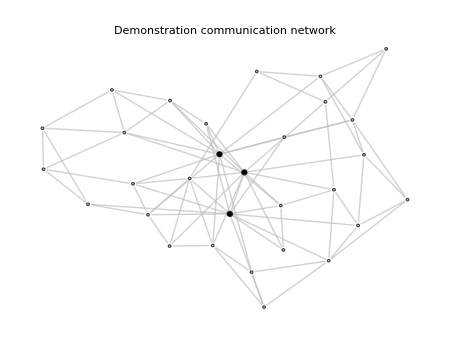

```mathematica
(* ::Section::*)
(*Generate demonstration network*)
ClearAll[demoNetworkData,demoNetworkSummary,demoGraph];

demoNetworkData=BuildNetworkData[demoNetSpec];
If[Head[demoNetworkData]===Failure,Print[demoNetworkData];
Abort[];];

demoNetworkSummary=NetworkSummary[demoNetworkData];
demoGraph=Graph[demoNetworkData["Graph"],VertexStyle->Join[Thread[demoNetworkData["Agents"]->GrayLevel[0.75]],Thread[demoNetworkData["MediaNodes"]->Black]],VertexSize->Join[Thread[demoNetworkData["Agents"]->Small],Thread[demoNetworkData["MediaNodes"]->Medium]],EdgeStyle->GrayLevel[0.75],GraphLayout->"SpringElectricalEmbedding",ImageSize->450,PlotLabel->"Demonstration communication network"];

Grid[{{"Vertices",demoNetworkSummary["VertexCount"]},{"Edges",demoNetworkSummary["EdgeCount"]},{"Density",N[demoNetworkSummary["Density"],4]},{"Mean degree",N[demoNetworkSummary["MeanDegree"],4]},{"Ordinary agents",demoNetworkSummary["AgentCount"]},{"Media/institutional nodes",demoNetworkSummary["MediaNodeCount"]},{"Mean agent degree",N[demoNetworkSummary["MeanAgentDegree"],4]},{"Mean media degree",N[demoNetworkSummary["MeanMediaDegree"],4]}},Frame->All,Alignment->Left];
demoGraph
```

```mathematica
(* ::Section::*)
(*Initialize diffusion process*)
ClearAll[demoSourceSpec,demoInitialCondition,demoInitialCounts];

demoSourceSpec=<|"nMisinformationSources"->2,"MisinformationSourceMethod"->"Random","Seed"->98765|>;
demoInitialCondition=BuildInitialCondition[demoNetworkData,demoSourceSpec,demoParams];
If[Head[demoInitialCondition]===Failure,Print[demoInitialCondition];
Abort[];];

demoInitialCounts=Counts[Values[demoInitialCondition["InitialStates"]]];
Grid[{{"Misinformation sources",demoInitialCondition["SM"]},{"Initial uninformed nodes",Lookup[demoInitialCounts,"U",0]},{"Initial misinformed nodes",Lookup[demoInitialCounts,"M",0]},{"Initial informed nodes",Lookup[demoInitialCounts,"I",0]},{"Campaign activation time",demoParams["tau"]}},Frame->All,Alignment->Left]
```

Misinformation sources | {27,15}
Initial uninformed nodes | 28
Initial misinformed nodes | 2
Initial informed nodes | 0
Campaign activation time | 5

```mathematica
(* ::Section::*)
(*Run simulation and compute outcomes*)
ClearAll[demoRun,demoMetrics,demoTimeSeries,demoSummaryRows];

demoRun=RunSingleSimulation[demoNetworkData,demoInitialCondition,demoParams,1];
If[Head[demoRun]===Failure,Print[demoRun];
Abort[];];

demoMetrics=ComputeRunMetrics[demoRun];
If[Head[demoMetrics]===Failure,Print[demoMetrics];
Abort[];];

demoTimeSeries=demoMetrics["TimeSeries"];

demoSummaryRows={{"Initial misinformed agents",demoMetrics["InitialM"]},{"Final misinformed agents",demoMetrics["FinalM"]},{"Final misinformation prevalence",N[demoMetrics["FinalMuM"],4]},{"Peak misinformation prevalence",N[demoMetrics["PeakMisinformation"],4]},{"Time of peak misinformation",demoMetrics["TimeOfPeakMisinformation"]},{"Clearance time",demoMetrics["ClearanceTime"]},{"Post-peak clearance time",demoMetrics["PostPeakMuClearanceTime"]},{"Information-dominance time",demoMetrics["InformationDominanceTime"]},{"Terminal misinformation slope",N[demoMetrics["TerminalMisinformationSlope"],5]}};

Grid[Prepend[demoSummaryRows,{"Metric","Value"}],Frame->All,Alignment->Left]
```

Metric | Value
Initial misinformed agents | 2
Final misinformed agents | 1
Final misinformation prevalence | 0.037037
Peak misinformation prevalence | 0.962963
Time of peak misinformation | 5
Clearance time | Missing[NotObserved]
Post-peak clearance time | 37
Information-dominance time | 15
Terminal misinformation slope | -0.0136684

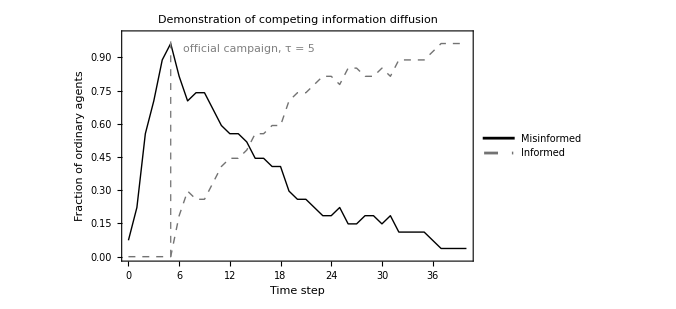

```mathematica
(* ::Section::*)
(*Visualize diffusion dynamics*)
ClearAll[demoMisinformationSeries,demoInformationSeries,demoDynamicsPlot];

demoMisinformationSeries=Transpose[{Lookup[demoTimeSeries,"t"],Lookup[demoTimeSeries,"muM"]}];
demoInformationSeries=Transpose[{Lookup[demoTimeSeries,"t"],Lookup[demoTimeSeries,"muI"]}];

demoDynamicsPlot=ListLinePlot[{demoMisinformationSeries,demoInformationSeries},PlotStyle->{Directive[Black,Thick],Directive[GrayLevel[0.45],Thick,Dashed]},PlotLegends->{"Misinformed","Informed"},Frame->True,Axes->False,FrameLabel->{"Time step","Fraction of ordinary agents"},PlotRange->{{0,demoParams["Tmax"]},{0,1}},Epilog->{Directive[GrayLevel[0.5],Dashed],Line[{{demoParams["tau"],0},{demoParams["tau"],1}}],Inset[Style[Row[{"official campaign, τ = ",demoParams["tau"]}],11],{demoParams["tau"]+1.5,0.94},Left]},ImageSize->500,PlotLabel->"Demonstration of competing information diffusion"];

demoDynamicsPlot
```

```mathematica
(* ::Section::*)
(*Export demonstration outputs*)
ClearAll[demoTimeSeriesTable,demoMetricsTable,demoTimeSeriesFile,demoMetricsFile,demoPlotFile];

demoTimeSeriesTable=Prepend[(Lookup[#,{"t","U","M","I","muM","muI"}]&)/@demoTimeSeries,{"t","U","M","I","muM","muI"}];
demoMetricsTable=Prepend[demoSummaryRows,{"Metric","Value"}];
demoTimeSeriesFile=FileNameJoin[{$DemoOutDir,"demo_time_series.csv"}];
demoMetricsFile=FileNameJoin[{$DemoOutDir,"demo_run_metrics.csv"}];
demoPlotFile=FileNameJoin[{$DemoOutDir,"demo_dynamics.png"}];

Export[demoTimeSeriesFile,demoTimeSeriesTable,"CSV"];
Export[demoMetricsFile,demoMetricsTable,"CSV"];
Export[demoPlotFile,demoDynamicsPlot,"PNG",ImageResolution->180];

Print["Demonstration outputs written to: ",$DemoOutDir];
```

Demonstration outputs written to: C:\Users\User\Desktop\temp\code_release\demo_output